Geometric Brownian motion - a model for the stock price fluctuations

S(t) =  ⅇ^(x + ν t+σ X(t)) = s_0ⅇ^(ν t+σ X(t)), where X(t)  is a standard Brownian motion  (X(t) ~ N(0, t) ),  s_0= S(0) = ⅇ^x,  is called a geometric Brownian motion and is widely used in modelling the fluctuations of the stock prices.  
Since  σ X(t) ~ N(0, σ^2 t),  E S(t) = E s_0 ⅇ^(ν t+σ X(t)) = s_0 ⅇ^νtEⅇ^(σ X(t)) = s_0 ⅇ^(ν t + (σ^2 t)/2)= s_0ⅇ^((ν + σ^2/2)t).  In the absence of noise,  σ = 0,  S(t) =   s_0 ⅇ^(ν t)  becomes a compound interest formula for initial capital  s_0, t in years  and the interest rate  
ν = r = (APR %)/(100%)).  The geometric Brownian motion could  also be viewed as a generalized compound interest formula with 
a randomly  varying  return rate.  Namely, if  S(t) is the capital at time  t  then  S(t) satisfies the following SDE (stochastic differential equation) :

 (_(dS(t)))/(S(t))= μ dt + σ (dX(t))/(d t) dt ,  where (dX(t))/(d t)= white noise = formal derivative of Brownian motion X(t)  [which does not exist!]
 
 The above equation is usually written in either a differential form (SDE - Stochastic Differential Equation)
 
  dS(t)= μ S(t) dt + σ S(t) dX(t) 
  
  or in an integral form (Ito Integral)
  
  S(t) - S(0) = ∫_0^t μS(u)du  +  ∫_0^t σS(u)dX(u) 
  
The second integral with respect to the Brownian Motion dX(u) is the so-called Ito Integral which plays a key role in stochastic analysis such as Financial Calculus.
  
The parameter σ = volatility,  measures the deviation of the stock price from μ = average stock return rate.  The equation 
is usually abbreviated:   dS = μ S dt + σ S dX.  Notice that for  σ = 0  the solution to dS = μ S dt  is again the compound interest formula  S(t) =   s_0 ⅇ^(μ t).  

On the other hand,  for σ > 0,  by applying Ito's stochastic calculus,  the solution to dS = μ S dt + σ S dX is found to be   

S(t) =   s_0ⅇ^((μ - σ^2/2)t + σ X(t)) 

For 1 share of a given security  (e.g., stock, option, etc.) with initial value  s_0,  S(t) represents its future value given the average rate of return on  1 share  = μ  and volatility = σ during 1 year period.  

Furthermore,

  E S(t) = s_0 ⅇ^((μ - σ^2/2 )t) E ⅇ^(σ X(t)) =  s_0 ⅇ^((μ-σ^2/2 )t)  ⅇ^(σ^2/2 t) =  s_0 ⅇ^(μ t)
  
  
  i.e., the expected (= average)  return on stock  S(t)  is equal to the (non-random) return with rate μ.

Note. To take advantage of this formula one must first obtain a reasonable estimate of the future values of the parameters 
(μ,  σ)  which could be a non-trivial exercise (may even  border with the insider-trading information, thus bearing inherent risks!).

```mathematica
Clear[s0,ν,σ,t,h];
```

```mathematica
BrownianGeometric[s0_,ν_,σ_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i]=sums[[i+1]],{i,0,m}];
geometric=Table[{i*h,s0*ⅇ^(ν *i*h+σ*X[i])},{i,0,m}];
drift=Table[{i*h,s0*ⅇ^(i*h * (ν +σ^2/2))},{i,0,m}];
g1=ListPlot[geometric,Joined->True,DisplayFunction->Identity,PlotRange->{0,50}];
g2=ListPlot[drift,Joined->True,DisplayFunction->Identity,PlotRange->{0,50}];
Show[{g1,g2},DisplayFunction->$DisplayFunction]]
```

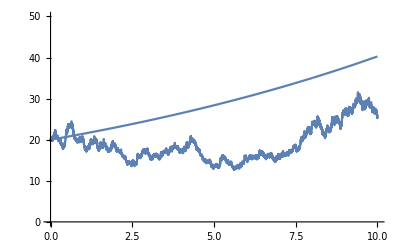

```mathematica
BrownianGeometric[20,.05,.2,10,.001]
```

The Black - Scholes Option Pricing Formula

One of the most celebrated results in the area of Finance is option pricing for the period prior to the option expiration.
A basis for the model is the generally accepted absence of arbitrage.  An arbitrage is a risk-free profit making scheme 
which takes advantage of the inefficiencies in financial markets resulted from securities valuation based upon Present-Future frame of reference. The reasoning for the absence of arbitrage stems from the assumption that traders, would take instantaneous advantage of such opportunities and therefore profiting from such schemes would have been short-lived and evaporated quickly.  An additional reason is that the knowledgeable traders would neither buy the overpriced securities nor would they sell securities below the actual price.  There is a contention that the bidding (buyers) price < actual price < and asking prices (sellers) are approximately the same. Otherwise it would lead to relatively few arbitrage opportunities, due to 
the fact that there would be no buyers or sellers to make it happen among knowledgeable market participants.  Of course, 
an arbitrage takes place whenever amateur investors are buying the overpriced securities from profiteering sellers or the amateurs are selling securities below their actual price to profiteering pros.  Observe that all knowledgeable investors,  in 
the absence of the insider trading information , would value traded security equally,  and consequently arbitrage would  
be impossible.   In other words, the absence of arbitrage leads to valuation that eliminates a risk-free profit.

A Call option with strike price K and the expiration time T is the right (but not an obligation) to buy 1 share of stock 
at the price K, called the strike price,  at the future time T.  Buying an option comes at a price C and the problem is to determine what  C  should be in the absence of arbitrage.  Options (which are examples of  derivatives on stocks) return profit only when the stock price  S(T)  at time T exceeds the strike price  K, in which case the option buyer will have 
gain = max [ S(T) - K, 0 ] ≥ 0  giving the net payoff = max [ S(T) - K, 0 ] - C.  It is important to point out the leverage 
on returns the option trading provides.  The risk associated with buying options is much higher than with buying the 
common stocks, however it is compensated by a potential reward  of  an n-fold return on a small initial investment.

Observe that the time value of money has intrinsically built-in a risk-less return rate  r /year  such as bonds or CD's (this being equivalent to earning a continuously compounded interest of  100 r %).  The present value of  v  to be paid at the future time T is only worth  v ⅇ^(-r T) < v  ( ⅇ^(-r T) = the discount factor),  for if   v ⅇ^(-r T) was available at present and loaned 
at the interest  r  during [0, T] it would accumulate to  v = (v ⅇ^(-r T))ⅇ^(r T)  by time  T.

Given the stock price process  S(u) = S(t)ⅇ^((μ-σ^2/2)(u-t)+σ (X(u)-X(t))),  0 ≤  t  ≤ u  ≤  T , Black - Scholes  Call option price C(t)  at time t, reads


(B-S)    C(t) =  E[ ⅇ^(-r (T-t))max [ Z(T) - K, 0 ]  = S(t) Φ(((r   + σ^2/2)(T-t) + l n((S(t))/K))/(σ √(T-t)))  - K ⅇ^(-r(T-t))Φ(((r - σ^2/2)(T-t) + l n((S(t))/K))/(σ √(T-t)))

      
where  Z(u) = S(t)ⅇ^((r - σ^2/2)(u-t)  + σ (W(u)-W(t)))  ,   with  E Z(u) = S(t) ⅇ^(r (u-t))  ,   W(.) = standard Brownian motion,
K = strike price,  T- t = expiration time in years , r = risk free return rate and  Φ(z) = ∫_(-∞)^z 1/(√(2π))ⅇ^(-x^2/2)dx = cumulative standard normal distribution ~ N(0,1).
 
Remark 1.   C(t) depends on the present stock price S(t), stock volatility  σ, the risk-free return rate  r, time till expiration  
T- t.  Surprisingly, C(t)  is independent of the stock's mean return rate  μ  (the measure of investor’s risk preferences).  
(B-S) says that in the risk-neutral world (investors demand only the expected return on investment to match the return on the risk-free interest rate r , i.e., investors are neutral toward risk,  as on average there is no risk!) the present option value C(t) is the discounted to present (= ⅇ^(-r (T-t))) expected future option value  E[max [ Z(T) - K, 0 ] derived from the risk-neutral stock  Z(t).
 
To explain how one arrives at (B-S), a concept of a fair game whose outcomes are left to chance is needed. 
 
The game is fair if the game's expected future gain [given all game history till present]  is zero.  That is, 

                             E [future Fortune(unknown) - present Fortune(known) | given known past] = 0 

In other words,  one cannot increase on average the future gains left to chance.    

Suppose that a combination of  buying and selling of stocks and options (on the underlying stock) takes place at time t and then selling and buying closes the underlying positions at time T. The problem is to find the option price  C(t)  to exclude the arbitrage opportunities.  

	In mathematical terms, the absence of arbitrage is equivalent to the existence of a probability measure P on all possible outcomes of an observable process (such as price of a given stock) which makes betting schemes on outcomes of this process (such as betting on the stock price itself or betting on the option price for this stock) simultaneous fair games!  

In this context the process that is being observed is the stock  price  S(t) = s_0ⅇ^((μ - σ^2/2)t + σ X(t)), 0 ≤ t ≤ T. 


Notice that (μ - σ^2/2)t + σ X(t) lives on the subset of continuous functions  ℂ[0,T].  Since the trajectories of the Brownian motion X(t)  are continuous this process is uniquely determined by two parameters (μ, σ) and determines a unique probability measure P^(X, μ, σ)on its trajectories = ℂ^(^(X, μ, σ))[0,T]⊂  ℂ[0,T].   Generally, for any given value ν,  W(t) = standard Brownian Motion, ν t + σ W(t)  gives rise to a random process and determines a unique probability measure P^(W, ν, σ)on its trajectories = ℂ^(^(W, ν, σ))[0,T]⊂  ℂ[0,T] .  It turns out that ℂ^(^(X, μ, σ))[0,T] = ℂ^(^(W, ν σ))[0,T] ≡ Ω  ⊂ ℂ[0,T].  Consequently, the processes

 S(t) =s_0ⅇ^((μ - σ^2/2)t + σ X(t))     and     Z(t) = s_0ⅇ^(ν t + σ W(t))  
 
 
live on the same set of possible outcomes.   In fact the probability measures  P^(W, ν, σ) and P^(X, μ, σ) are related through a strictly positive density function  Λ (X) such that  dP^(W, ν, σ)= Λ (X) dP^(X, μ, σ) (a version of change of variables/measures, known as Girsanov-Cameron-Martin Formula)

Consider the following 2 betting games contingent upon the future stock price as follows:

Game I  :   bet   $1      on the stock with  Payoff  I  = ⅇ^(-r T)S(T) - ⅇ^(-r t)S(t) ,    0 ≤  t ≤ T  (buy at time t sell at time T)
Game II :  bet   $C(t)  at time t on the stock price at time T with  Payoff  II = ⅇ^(-r (T-t))max [ S(T) - K, 0 ] - C(t) , 0 ≤ t ≤ T

Notice that in both cases the Payoff is in Present Value (i.e., discounted values compensated by the risk-free return rate r ).
     
To eliminate arbitrage it suffices to find a probability measure P, or equivalently a random process  Z  on  Ω , that makes both games fair.  

Conditioning  E[Payoff  I | past] =  E[ⅇ^(-r t)Z(t) - ⅇ^(-r s)Z(s) | Z(s) = z(s), Z(u) = z(u),  0 ≤ u < s ] = 0. 

This means E[ⅇ^(-r t)Z(t) | Z(s) = z(s), Z(u) = z(u),  0≤ u < s ] = ⅇ^(-r s)z(s)  

or

  E[ ⅇ^(-r t)Z(t) | Z(u), 0≤ u ≤ s ] = ⅇ^(-r s)Z(s) 

 Equivalently,  ⅇ^(-r t)Z(t)  must be a martingale.  
 
 This requires for  Z(t) =  s_0ⅇ^(ν t + σ W(t))   that  ν = r - σ^2/2 
  
Namely, 

Z(t) =  s_0ⅇ^((r-σ^2/2 )t + σ W(t)) ,  which  gives  EZ(t) = s_0 ⅇ^((r-σ^2/2 )t) Eⅇ^(σ W(t)) =  s_0ⅇ^(r t)


i.e., the expected return on  Z(t) is equal to the return on the risk-free interest r.  

Therefore, the process {Z(u),   t ≤ u ≤ T} has the form

Z(u) = S(t) ⅇ^((r-σ^2/2 )(u-t )+ σ (W(u)-W(t)))    ,   for t≤ u ≤ T

The expected gain from betting on the option must then also be 0.  That is

 E[Payoff  II|past] = E[ ⅇ^(-r (T-t))max [ Z(T) - K, 0 ] - C(t) ] = 0, 
 
 which is the same as

C(t) =  E[ ⅇ^(-r (T-t))max [ Z(T) - K, 0 ]  

and upon evaluation gives the Black-Scholes pricing  (B-S)  above.

Remark 2.  One shall keep in mind that process  Z(t) =  s_0ⅇ^((r - σ^2/2)t + σ W(t)) serves exclusively the purpose of proving the existence of  the absence of arbitrage and allows to determine the option price  C(t)  given in (B-S).  The only reason the name W(t) for standard Brownian motion was chosen here was to make a clear distinction between the actual observable stock price process S(t) and the "artificial stock price process"  Z(t)  ( obtained from  S(t) = s_0ⅇ^((μ - σ^2/2)t + σ X(t)) by  simply setting  μ = r and corresponds to  dS = r S dt + σ S dX , as opposed to actual stock process equation dS = μ S dt + σ S dX).

 It doesn't matter whether one uses W(t) or X(t) to define process Z(t) as both are standard Brownian motions .  Observe that Z(t) is not the actual stock price process as Z(t) does not incorporate the investor's risk measure μ, whereas S(t) does.   Z(u) only connection to S(u)  in the (B-S) is through the present stock price Z(t) = S(t), whereas for  t ≤ u  ≤T  the evolution of  S(u) and Z(u)  are different.  Namely, return rate μ of the actual stock price S(t) differs from the risk-free rate r in Z(t).  

It is a pure coincidence but a consequence of the absence of arbitrage,  that the future average rate of return  μ  on the stock plays no role in calculating the fair present value of the option  C(t).  Consequently, one does not need to know the future average return rate  μ on the stock to determine the fair present price of the option.  The only thing that matters is the volatility  σ  of the stock price S(t).  Since  C(t) in (B-S) is an increasing function of the volatility  σ (can be checked by differentiation) it appears that the option valuation is in full agreement with an old adage: "the money is where the action is".  Namely,  the more volatility in the market (sudden big uncertainty affecting equilibrium) the better the opportunity to profit (for some) and lose (for others).  And, of course, not risk-free!

Below is a an example of the European Call Option valuation with  C(t) = OptionValue[t, T, Xt, K, σ, r]

```mathematica
Φ[x_]:=CDF[NormalDistribution[0,1],x];
```

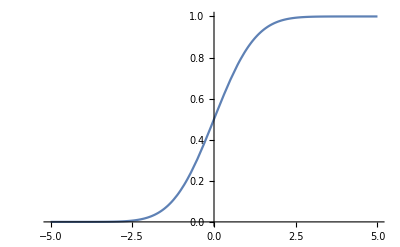

```mathematica
Plot[Φ[x],{x,-5,5}]
```

```mathematica
OptionVal[t_,T_,Xt_,K_,σ_,r_]:=
Xt*Φ[((r+σ^2/2)*(T-t)+Log[Xt/K])/(σ √(T-t))]-K ⅇ^(-r*(T-t))*Φ[((r-σ^2/2)*(T-t)+Log[Xt/K])/(σ √(T-t))];
```

Consider a stock XYZ that is presently trading at $415/8/share and one wants to buy a  6 months (t = 1/2 year) Call option with the strike price K = $40.  Assuming  30% volatility in the stock price ( σ = . 30)  and  the prevailing  rate of return on 
risk-free investment  r = .02,  the fair price for this Call option at time  s = 0  is

```mathematica
OptionVal[0,1/2,41.625,40.,.30,.02]
```

4.53593

If  2 months later (s = 2/12) the stock value drops to  $345/8 (16.8%  drop)  then the option value drops as well  however by 83%  (about 5 - fold compared to a drop in the stock price)

```mathematica
OptionVal[1/6,1/2,34.625,40.,.30,.02]
```

0.777863

### Detailed examples of auxiliary Z(t) process and it’s shadowing C(t) option process

Below are simulations of the process Z(t) = s_0ⅇ^((r - σ^2/2) t + σ X(t))and calculation of option prices C(t)  during a half-year period.  Here  s_0= 41.625,  σ = .3,  r = .02, K= 40, T=.5.   
It shows how the option prices C(t)  mimic the stock process Z(t) but on a different scale (more volatility).

At the expiration time the return on the option would be (8.70-4.53)/4.53100% = 92%.  Suppose now that a person A bought 50 shares of  XYZ (i.e. invested total of 50 x  $415/8= $ 2,081).  A half year later A would be worth 50 x $ 48.8 = $2,440 or made profit of  $359  or  17.25% (in 6 months).  Suppose that a person  B did not have the $ 2,081 person A had, and instead B decided to invest 
all of  $453 available and  bought 100 options @ $4.53/option.  At the option expiration time B would be worth  $870 or made a profit of $417 or 92%.  The clear leverage of trading options is this:  B having only $453 at hand could beat A with $2,081 at hand by making a profit of  $417  versus  $359.  If  a person C, having  $ 2,081 at hand,  invested everything in options than thanks to 92% return on options C would be worth $3,995 in six month or made a profit of $1,914.

Remark 3.  Unlike the option studied above (the so - called European option, i.e., the option the  buyer must hold till its expiration),  the American option allows for selling the option at any time prior to the expiration.  As one can see,  the return on American option is  generally higher and in our example above would be almost 8 - fold the return on the stock.  Namely,  after about 3 months the return on the option  (if sold) would have been (21.6-4.53)/4.53100% = 376 %  as opposed to the return on selling  stock (61.6-41.6)/(41,6)100%  = 48 %.  This would mean that in this case (when closing the deal after 3 months)  A (starting with $2081) would be worth $3080,  B (starting with $453) would be worth $2,160 and C (starting with $2081) would be worth $2081/$4.53  (= number of options bought) x $ 21.6(= option value) = $9,914 !

On the other hand, when XYZ  price moves below the strike price K shortly before the expiration time  t,  then the  option value dissipates quickly to 0 and becomes worthless as the graph below shows

WARNING.  The above examples illustrate a special case in which  S(t) =Z(t), or equivalently, μ (the stock return rate) = r (risk free return rate).

### Implementation of simulation of Z (t) and C (t)

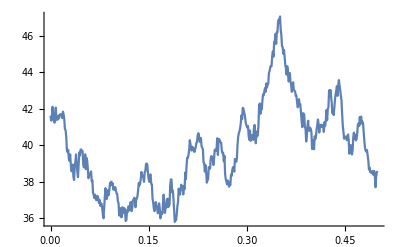

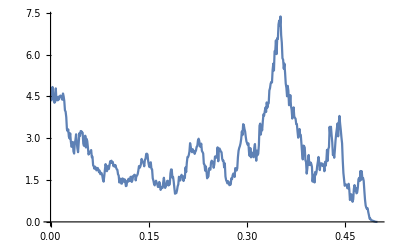

```mathematica
StockGrowth[z0_,r_,σ_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i]=sums[[i+1]],{i,0,m}];
geometric=Table[z0*ⅇ^((r -σ^2/2)*i*h+σ*X[i]),{i,0,m}]]
StockGrowth[41.625,.02,.30,.5,0.001];
Xt=geometric;m=500;h=.001;         (* stock prices 0 ≤ t ≤ T =.5  *)
g1=Table[{i*h,Xt[[i+1]]},{i,0,m}];
ListPlot[g1,Joined->True];

OpVal=Table[{h*i,OptionVal[h*i,.5,Xt[[i+1]],40.,.30,.02]},{i,0,m-1}];

ListPlot[g1,Joined->True]
ListPlot[OpVal,Joined->True]
```

### Implementation of simulation of actual stock process S(t) and its option process C (t)

If one wants a simulation of the actual stock price process  S(t) = s_0ⅇ^((μ - σ^2/2)t+σ X(t))  one has to take a risk and assume a specific future value of  μ = average future return rate.  Below are simulations for  μ = . 25  (25% return), r = .04  (4% interest rate) with two different outcomes: first winning,  the second loosing big!

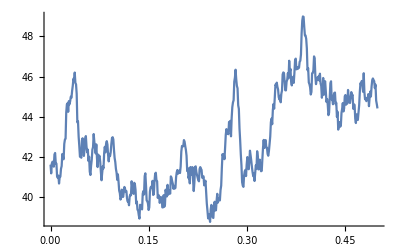

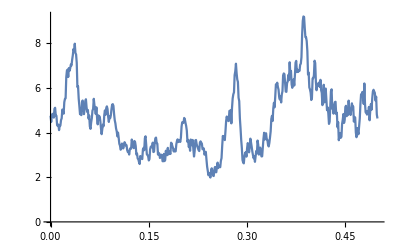

```mathematica
StockGrowth[s0_,μ_,σ_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i]=sums[[i+1]],{i,0,m}];
geometric=Table[s0*ⅇ^((μ -σ^2/2)*i*h+σ*X[i]),{i,0,m}]]
StockGrowth[41.625,.25,.30,.5,0.001];
Xt=geometric;m=500;h=.001;         (* stock prices 0 ≤ t ≤ T =.5  *)
g1=Table[{i*h,Xt[[i+1]]},{i,0,m}];
ListPlot[g1,Joined->True];

OpVal=Table[{h*i,OptionVal[h*i,.5,Xt[[i+1]],40.,.30,.04]},{i,0,m-1}];

ListPlot[g1,Joined->True]
ListPlot[OpVal,Joined->True]
```

### Estimating μ and σ from historical stock data

Stock price with average annual return  μ  and  volatility σ follows the geometric Brownian motion  S_t = S_0 e^(e^((μ-1/2 σ^2)t + σX_t)). 
To estimate (μ, σ) one uses daily closing price at times  days  d = 1, 2,....  (1 year = 52 weeks = 260 days, but on average about 252 trading 
days (due to holidays). Therefore, time period of 1 day corresponds to the time duration of  1/252,  given time unit = 1 year).

Given S_0,  n = # of days trading days during the time periot [0, t] with t  in years, and recorded stock prices in days  d = 1,2,...n  

Y_d = Log[S_d/(S_(d-1))] = (μ-1/2 σ^2)Δ+ σ(X_d - X_(d-1))Δ   ~ N ((μ-1/2 σ^2)Δ, σ^2Δ),    where  Δ = t/n      X_d - X_(d-1)  ~  N(0,1)

Then by the Law of Large Numbers

(Y_1+Y_2+...+Y_n)/n  →     (μ-1/2 σ^2)Δ    and     Variance ((Y_1+Y_2+...+Y_n)/n)  →  σ^2Δ   or  Standard deviation ((Y_1+Y_2+...+Y_n)/n)  → σ√Δ ,  for large n

can be used as approximations to  (μ, σ).


REMARK [ Mathematica built-in functions]

Given  data = {x_1,...,x_n} sampled from a random variable  X 

Mean [data]  =  x̄  =  1/n∑_i x_i  =  average value
StandardDeviation [data]  = √(1/(n-1)∑_i (x_i-x̄)^2)  = unbiased estimator of the true standard deviation  
σ = √(σ^2) = √(EX^2-(EX)^2)

#### Example

Below is the stock data from Google [GOOG = stock ticker symbol for Google] obtained from google webstite 
[or other websites:  http://www.quantshare.com/sa-43-10-ways-to-download-historical-stock-quotes-data-for-free ]

with the syntax as follows:

http://www.google.com/finance/historical?output=csv&q=GOOG

and saved as filename.csv [MS Excel, for example, reads this file].  

Open filename.csv ,  select the column of numbers of interest,  paste it into MS Notepad [or ony other pure text editor using exclusively ASCII, i.e.,  does not include any formatting characters!], and save as filename.txt

Then read the filename.txt into Mathematica notebook for further analysis.

```mathematica
(* Import file [Mathematica syntax]: 
data=ReadList["C:\Users\[type user name]\Desktop\filename.txt",Number]*)

(* downloaded data is usually from newest to oldest so one must use Reverse[downolaed data]
to reverse the list [from oldest to newest] to get correct analysis *)
```

```mathematica
data
```

{537.43,539.12,538.56,536.08,535.79,534.27,535.3,537.68,542.66,535.45,536.2,529.55,518.42,530.46,529.81,531.25,524.03,518.39,518.26,519.67,518.13,520.9,529.02,525.6,528.06,526.35,521.06,519.03,519.17,516.73,509.5,505.,508.37,502.95,500.37,485.02,484.58,493.,487.,480.22,474.88,482.8,493.65,497.57,506.38,521.03,532.44,535.36,546.6,531.99,527.28,534.01,538.26,528.94,597.62,594.94,602.55,595.35,606.99,618.23,618.98,622.52,607.22,610.94,603.69,606.77,592.4,601.17,577.52,579.04,546.02,573.41,549.01,562.13,563.77,557.23,539.,533.15,504.88,490.92,498.17,518.82,523.29,520.04,526.86,539.08,540.7,540.96,532.5,524.84,522.18,534.03,534.96,524.85,530.12,529.52,532.07,542.56,546.68,546.67,546.62,539.2,520.66,525.51,531.89,539.34,528.84,527.5,515.04,495.52,501.9,504.7,514.71,515.12,537.17,543.18,548.5,558.99,591.68,582.41,590.51,580.7,583.67,590.49,596.42,583.16,586.31,598.67,600.14,592.64,578.65,584.82,597.5,596.14,608.33,612.34,600.95,595.08,608.35,613.,616.56,611.47,600.87,594.88,580.94,580.,570.11,563.,588.19,582.93,599.39,613.77,620.36,625.65,623.77,623.39,616.05,627.42,625.39,625.63,618.07,619.54,625.96,621.83,630.37,625.82,629.7,631.88,640.25,639.7,642.4,645.9,665.41,668.28,659.01,652.73,622.46,623.14,625.96,629.64,624.99,628.58,632.91,639.57,585.99,585.52,580.93,569.49,568.1,579.98,577.69,580.11,580.83,585.11,596.33,609.09,606.77,609.7,611.46,605.91,612.2,609.76,605.56,606.52,604.64,614.,607.94,606.11,609.9,609.31,618.39,618.25,622.4,621.25,614.25,604.96,606.8,607.14,600.25,605.15,617.78,615.99,621.13,625.04,633.98,633.49,639.98,646.05,642.59,649.33,647.02,655.76,648.41,641.24,646.92,642.62,635.15,632.32,630.84,626.86,635.96,651.01,624.6,606.07,609.57,607.45,599.3,596.06,597.6,601.27,609.72,615.47}

```mathematica
Length[data]  (* we assumed n=252 trading days in t=1 year or Δ=1/252; t=1, n=252, Δ=t/n *)
```

252

```mathematica
dat2=Table[Log[data[[k]]/data[[k-1]]],{k,2,Length[data]}]//N; 
   
(* dat2 = {Subscript[y, 1],..., Subscript[y, 251]} has 251 elements obtained from ratios of Subscript[X, d], d=1,2,..., 252 days *)
```

```mathematica
Mean[dat2]  (* estimate of  (μ -1/2 σ^2)Δ  *)
```

0.00054019

```mathematica
StandardDeviation[dat2] (* estimate of σ √Δ  *)
```

0.0187491

To obtain annualized estimates for (μ -1/2 σ^2) and  σ  one must divide the above obtained values by  Δ  and √Δ  respectively

```mathematica
252Mean[dat2]  (* estimate of  μ -1/2 σ^2 *)
```

0.136128

```mathematica
0.13612787459140058  (* estimate of  μ - 1/2 σ^2  ~ annual return of 13.6 % *)
```

```mathematica
√252 StandardDeviation[dat2]//N    (* estimate of σ *)
```

0.297632

```mathematica
0.297632412819663    (* estimate of σ  ~ annual volatility of 29.8 % *)
```

Estimate of  μ   [based on the above estimates and  μ   =  (μ - 1/2 σ^2)  + 1/2 σ^2 ]

```mathematica
0.13612787459140058 +1/2(0.297632412819663  )^2
```

0.18042

```mathematica
(* estimate of μ  ~ annual return of 18 % *)
```

## Stock Options Quotes

Stock options quotes are readily available online, for example at

```mathematica
http://www.cboe.com/DelayedQuote/DQBeta.aspx
```

The Chicago Board Options Exchange (CBOE)

The largest U.S.options exchange and creator of listed options, continues to set the bar for options trading through product innovation, trading technology and investor education.

Which risk free rate of return r% /year should be in the Black-Scholes Option Pricing Model?

### Answer: Academics typically use US Treasury rates. Practioners typically use swap rates or Libor. One may also use CD rates or Money Market rates [currently yielding about 1% /year]. All rates are readily available online.

LIBOR is the interest rate that banks charge each other for one - month, three - months, six - months and one - year loans. LIBOR is an acronym for London InterBank Offered Rate. This rate is that which is charged by London banks, and is then published and used as the benchmark for bank rates all over the world.

### REMARK

For any given strike price K, generally one choses a listed last trade [i.e., whenever underlying Call Option is currently actively traded and falls between the bid  and ask price range].  If the listed last trade is out of  [bid , ask] range (meaning the last trade is an old data), then the average of bid and ask price is a reasonable Call Option value.